```mathematica
SetDirectory["/Users/brucesawhill/Desktop/DayJetDesktop/2006_Census"]
```

/Users/brucesawhill/Desktop/DayJetDesktop/2006_Census

```mathematica
FileNames[]
```

{.DS_Store,ModelQuadBuffers_50_100mile_Dem2006.csv,ModelQuad_Dem2006.csv,ModelQuad_Dem2006.csv.desc.txt,ModelQuad_GreaterSE_2006.csv,sedriverlist}

This whole analysis is based on Sinam's grid-square data that gives total pop, wealth classes (by household) and the source and sink subpopulations for each grid square and a 50 and 100-mile radius around said grid square.

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/MathematicaData"]
```

/Users/brucesawhill/Desktop/MathematicaData

```mathematica
FileNames[]
```

{150hubpop,2way,3parameterloglinearfit,3parameterloglinearinversewtfit,3parameterloglinearnowtfit,75hubpop,airports,allgrid,arr1,asymodpairsbizplus,asymodpairsbizplusfilter,asympairlist,asypairspeopledistbizplus,ats95allincomes,attrmatrix,auto,battrmatrix,battrmatrix.XLS,bintripmatrix,bintripmatrix.XLS,bizplotpairs,bizprecise,bizspendintensityptsusa04,bizspendintensityusa04,bizstars,bkstail,bouttripmatrix,bouttripmatrix.XLS,bts95mma,calibration750,characteristictimes,closebizports,corrmatrix,countmatrix,cumubizspendint,cumuleisspendint,drawusamma,.DS_Store,firmpops,flyratio,fmatrix,fpos,gravdata,griddata2006,hoursvisits,hyperpts,incomespendpts,intripmatrix,leisureplotpairs,leisureprecise,leisurewealthtrips,measurebar,modeproportions,msadistancetable,msahosp04,msaincomesmod03,msaintrips2000,msaleisuredata,msaleisuredatafilt,msaleisureintrips2000,msaleisureouttrips2000,msaleisurepairtrips2000,msaoccs04,msaoccsmod03,msaocctots04,msaonly,msaouttrips2000,msapops03,msapops0409,msapops48,msapopsmod03,mxvisit,newlistformat,noerrorfilteredflights,nonlinearfitinversewt,nonlinearfitlinearwt,nonlinearfitnowt,nonstops,nozeros,nozeros4k,odpairsbizplus,othertravel,outtripmatrix,pairspeopledistbizonly,pairspeopledistbizplus,phyloset,physicaljetairports,planeintrosched,planelist,popprodziptable,popzipsums,preplacement,r1ziplist,renormpairsmsa,return1,returnoneways,rmsaleisuredata,statsigprojector,sympairlist,tf,threematrix,tiabiztravbyincome,timearray,totalspend,totaltravel,travelscope06mma,travelscopejetsonleisure,tripsbyhhinccategory,tsimatrixbiz,tsmsa,uniquepositionlist,usa04,usamsa04,usazipsmma,ushubs,wealth,wealthpairs,wealthzips,websurveydata,whatwherewhen,winningregression,zipindices,zzbistars}

```mathematica
gridcts=<<griddata2006;
```

```mathematica
gridcts=Import["ModelQuad_Dem2006.csv","CSV"];
```

```mathematica
gridcts>>griddata2006;
```

```mathematica
Position[gridcts,"24082-E7"]
Position[gridcts,"24082-E8"]
Position[gridcts,"24082-F7"]
Position[gridcts,"24082-F8"]
```

{{167,2}}

{{168,2}}

{{169,2}}

{{170,2}}

```mathematica
Take[gridcts,{167,170}]
```

{{Dry Tortugas OE SE,24082-E7,0,0,0,0,0,-82.8125,24.5625,,,,,,,0,0,0,0,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0},{Dry Tortugas OE S,24082-E8,0,0,0,0,0,-82.9375,24.5625,,,,,,,0,0,0,0,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0},{Dry Tortugas OE E,24082-F7,0,0,0,0,0,-82.8125,24.6875,,,,,,,0,0,0,0,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0},{Dry Tortugas (digital),24082-F8,0,0,0,0,0,-82.9375,24.6875,,,,,,,0,0,0,0,0.,0.,0.,0.,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Take[gridcts,3]//MatrixForm
```

(NAME | KEY | ADULTCY | HHDCY | BUSCYEMP | BUSCYEST | INCCYAVEHH | CentroidX | CentroidY | KEY_STATE | NAME_STATE | KEY_METRO_CBSA | NAME_METRO_CBSA | KEY_MICRO_CBSA | NAME_MICRO_CBSA | IND00FOOD | IND00CONS | IND00PUBA | IND00REAL | XCYTR801 | XCYTR803 | XCYTR5 | XCYTR8 | HHIncLessthan10K | HHinc10K20K | HHinc20K30K | HHinc30K40K | HHinc40K50K | HHinc50K60K | HHinc60K75K | HHinc75K100K | HHinc100K125K | HHinc125K150K | HHinc150K200K | HHinc200Kplus
Ka Lae (digital) | 18155-H6 | 54 | 28 | 119 | 19 | 42410 | -155.687 | 18.9375 | 15 | Hawaii |  |  | 25900 | Hilo, HI Micro | 2 | 3 | 0 | 1 | 288.84 | 77.65 | 1860.25 | 448.95 | 5 | 4 | 2 | 3 | 2 | 2 | 2 | 1 | 1 | 0 | 0 | 1
Puu Hou (digital) | 18155-H7 | 0 | 0 | 0 | 0 | 0 | -155.812 | 18.9375 |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dimensions[gridcts]
```

{54013,35}

```mathematica
gridcts50100=Import["ModelQuadBuffers_50_100mile_Dem2006.csv","CSV"];
```

```mathematica
Dimensions[gridcts50100]
```

{25271,35}

```mathematica
bufferkeys=
```

```mathematica
Take[gridcts50100,3]//MatrixForm
```

(NAME | KEY | ADULTCY | HHDCY | BUSCYEMP | BUSCYEST | INCCYAVEHH | CentroidX | CentroidY | KEY_STATE | NAME_STATE | KEY_METRO_CBSA | NAME_METRO_CBSA | KEY_MICRO_CBSA | NAME_MICRO_CBSA | IND00FOOD | IND00CONS | IND00PUBA | IND00REAL | XCYTR801 | XCYTR803 | XCYTR5 | XCYTR8 | HHIncLessthan10K | HHinc10K20K | HHinc20K30K | HHinc30K40K | HHinc40K50K | HHinc50K60K | HHinc60K75K | HHinc75K100K | HHinc100K125K | HHinc125K150K | HHinc150K200K | HHinc200Kplus
Ables Springs: 50.0 Miles | 32096-G1 | 2324560 | 1149954 | 1473442 | 140113 | 73088 | -96.0625 | 32.8125 | 48 | Texas | *19100 | *Dallas-Fort Worth-Arlington, TX Metro | * | * | 79794 | 111982 | 36441 | 35638 | 441.38 | 118.35 | 2525.27 | 685.17 | 61011 | 70927 | 97388 | 110705 | 91890 | 82083 | 108054 | 125409 | 84332 | 46026 | 40716 | 55612
Ables Springs: 100.0 Miles | 32096-G1 | 5276425 | 2585060 | 3014324 | 288453 | 67682 | -96.0625 | 32.8125 | *48 | *Texas | *19100 | *Dallas-Fort Worth-Arlington, TX Metro | * | * | 173475 | 237905 | 97318 | 69269 | 411.17 | 110.29 | 2434.12 | 638.31 | 137815 | 166043 | 221258 | 246654 | 209273 | 191111 | 250992 | 284632 | 184146 | 95638 | 81503 | 98055)

```mathematica
segrid=Import["ModelQuad_GreaterSE_2006.csv","CSV"];
```

```mathematica
Dimensions[segrid]
```

{10948,5}

```mathematica
Union[Table[Length[Position[gridcts50100,segridkey[[i]]]],{i,Length[segridkey]}]]
```

$Aborted

Check to see if the SE grid squares are a proper subset of the buffer data and all the other proper subsets are indeed proper subsets.

```mathematica
bufferkey=Table[gridcts50100[[i,2]],{i,2,Length[gridcts50100]}];
segridkey=Table[segrid[[i,3]],{i,2,Length[segrid]}];
gridkey=Table[gridcts[[i,2]],{i,2,Length[gridcts]}];Complement[segridkey,bufferkey]
Complement[segridkey,gridkey]
Complement[bufferkey,gridkey]
```

{}

{}

{}

These are the categories

```mathematica
gridcts[[1]]
```

{NAME,KEY,ADULTCY,HHDCY,BUSCYEMP,BUSCYEST,INCCYAVEHH,CentroidX,CentroidY,KEY_STATE,NAME_STATE,KEY_METRO_CBSA,NAME_METRO_CBSA,KEY_MICRO_CBSA,NAME_MICRO_CBSA,IND00FOOD,IND00CONS,IND00PUBA,IND00REAL,XCYTR801,XCYTR803,XCYTR5,XCYTR8,HHIncLessthan10K,HHinc10K20K,HHinc20K30K,HHinc30K40K,HHinc40K50K,HHinc50K60K,HHinc60K75K,HHinc75K100K,HHinc100K125K,HHinc125K150K,HHinc150K200K,HHinc200Kplus}

```mathematica
gridcts[[1,16]]
gridcts[[1,17]]
```

IND00FOOD

IND00CONS

Generate "The List"

```mathematica
segridkey[[1]]
```

33094-G8

```mathematica
segrid[[2]]
```

{Acworth,TX,33094-G8,-94.875,33.75}

```mathematica
sequad=Table[gridcts[[Position[gridcts,segridkey[[i]]][[1,1]]]],{i,1,Length[segridkey]}];
sequadbuffer=Table[gridcts50100[[Position[gridcts50100,segridkey[[i]]][[1,1]]]],{i,1,Length[segridkey]}];
```

```mathematica
Dimensions[sequadbuffer]
```

{10947,35}

```mathematica
gridcts[[1]]
```

{NAME,KEY,ADULTCY,HHDCY,BUSCYEMP,BUSCYEST,INCCYAVEHH,CentroidX,CentroidY,KEY_STATE,NAME_STATE,KEY_METRO_CBSA,NAME_METRO_CBSA,KEY_MICRO_CBSA,NAME_MICRO_CBSA,IND00FOOD,IND00CONS,IND00PUBA,IND00REAL,XCYTR801,XCYTR803,XCYTR5,XCYTR8,HHIncLessthan10K,HHinc10K20K,HHinc20K30K,HHinc30K40K,HHinc40K50K,HHinc50K60K,HHinc60K75K,HHinc75K100K,HHinc100K125K,HHinc125K150K,HHinc150K200K,HHinc200Kplus}

```mathematica
driverlist=Table[Join[sequad[[i]],{sequadbuffer[[i,16]]},{sequadbuffer[[i,17]]}],{i,Length[sequad]}];
```

```mathematica
FileNames[]
```

{.DS_Store,ModelQuadBuffers_50_100mile_Dem2006.csv,ModelQuad_Dem2006.csv,ModelQuad_Dem2006.csv.desc.txt,ModelQuad_GreaterSE_2006.csv,sedriverlist}

```mathematica
driverlist>>sedriverlist;
```

```mathematica
driverlist[[1]]
```

{Acworth,33094-G8,186,93,5,2,40783,-94.9375,33.8125,*40,*Oklahoma,,,,,7,4,5,1,275.96,74.04,1848.78,428.81,6,13,12,6,5,8,10,4,2,0,1,0,4130,6938}

```mathematica
sequad[[1]]
```

{Acworth,33094-G8,186,93,5,2,40783,-94.9375,33.8125,*40,*Oklahoma,,,,,7,4,5,1,275.96,74.04,1848.78,428.81,6,13,12,6,5,8,10,4,2,0,1,0}

```mathematica
Take[sequad[[1]],{24,35}]
```

{6,13,12,6,5,8,10,4,2,0,1,0}

```mathematica
income2001= {0,15,25,35,50,75,100,125,150,200,250}
```

{0,15,25,35,50,75,100,125,150,200,250}

```mathematica
trpropensity2001={0.293,0.513,0.785,0.977,1.261,1.7,1.596,1.406,1.642,1.258,0.669}
```

{0.293,0.513,0.785,0.977,1.261,1.7,1.596,1.406,1.642,1.258,0.669}

```mathematica
trpropensity={0.293,2/3 .513 + 1/3 .293, 1/2 (.513  +.785),1/2 (.785+.977),1/3 (.977) + 2/3 (1.261),1.261,.4 (1.261)+.6 (1.7),1.7,1.596,1.406,1.642,1.258}
```

{0.293,0.439667,0.649,0.881,1.16633,1.261,1.5244,1.7,1.596,1.406,1.642,1.258}

```mathematica
income= {0,10,20,30,40,50,60,75,100,125,150,200}
```

{0,10,20,30,40,50,60,75,100,125,150,200}

Let's do some exploratory analysis of how much the income exponent varies across grid squares.  First, calculate the exponent for the whole Southeast. Do this by computing cumulative populations above a certain income level and then use the old "travel propensity" calculation to weight for business travel.  Remember this data is for household income instead of individual income like the 2001 IRS data.  Note that in analyzing the 2006 Census data that the income boundaries are different.  This requires figuring out a new travel propensity vector by interpolation of the old one.

```mathematica
bizincomepops=Table[Take[driverlist[[i]],{24,35}],{i,Length[driverlist]}];
```

Note that travel propensity is from an old analysis and that the income breaks in the 2006 data don't match any more.  Hopefully in the future, travel propensity will be emergent and not imposed.

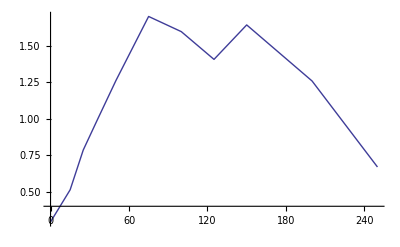

```mathematica
oldtr=ListPlot[Table[{income2001⟦i⟧,trpropensity2001⟦i⟧},{i,11}],Joined->True]
```

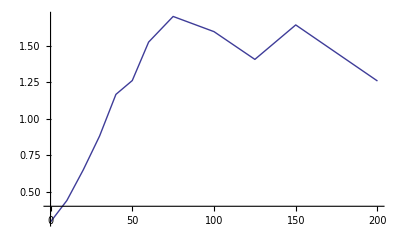

```mathematica
newtr=ListPlot[Table[{income⟦i⟧,trpropensity⟦i⟧},{i,12}],Joined->True]
```

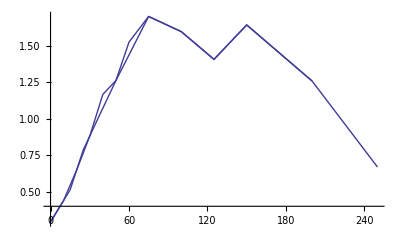

```mathematica
Show[oldtr,newtr]
```

```mathematica
hhwealthbins=Table[Sum[bizincomepops[[i,j]], {i,Length[bizincomepops]}],{j,1,12}]
```

{2402940,2645052,3181143,3302034,2776886,2529897,3138610,3180930,1834980,885671,711646,821738}

```mathematica
weightedbins=Table[hhwealthbins[[j]]trpropensity[[j]],{j,12}]
```

{704061.,1.16294×10^6,2.06456×10^6,2.90909×10^6,3.23877×10^6,3.1902×10^6,4.7845×10^6,5.40758×10^6,2.92863×10^6,1.24525×10^6,1.16852×10^6,1.03375×10^6}

```mathematica
cumulsums=Table[Sum[hhwealthbins[[i]],{i,j,12}],{j,1,12}]
```

{27411527,25008587,22363535,19182392,15880358,13103472,10573575,7434965,4254035,2419055,1533384,821738}

```mathematica
weightedcumulsums=Table[Sum[weightedbins[[i]],{i,j,12}],{j,1,12}]
```

{2.98379×10^7,2.91338×10^7,2.79709×10^7,2.59063×10^7,2.29972×10^7,1.97584×10^7,1.65682×10^7,1.17837×10^7,6.37615×10^6,3.44752×10^6,2.20227×10^6,1.03375×10^6}

```mathematica
plotpts=Table[{income[[i]],weightedcumulsums[[i]]},{i,12}]//N
```

{{0.,2.98379×10^7},{10.,2.91338×10^7},{20.,2.79709×10^7},{30.,2.59063×10^7},{40.,2.29972×10^7},{50.,1.97584×10^7},{60.,1.65682×10^7},{75.,1.17837×10^7},{100.,6.37615×10^6},{125.,3.44752×10^6},{150.,2.20227×10^6},{200.,1.03375×10^6}}

```mathematica
normplotpts=Table[{income[[i]],weightedcumulsums[[i]]/weightedcumulsums[[1]]},{i,11}]//N
```

{{0.,1.},{10.,0.976404},{20.,0.937428},{30.,0.868236},{40.,0.770739},{50.,0.662193},{60.,0.555275},{75.,0.394925},{100.,0.213693},{125.,0.115542},{150.,0.0738079}}

```mathematica
pdfbiz=Table[{income[[i]],weightedbins[[i]]/(income[[i+1]]-income[[i]])},{i,11}]//N
```

{{0.,70406.1},{10.,116294.},{20.,206456.},{30.,290909.},{40.,323877.},{50.,319020.},{60.,318966.},{75.,216303.},{100.,117145.},{125.,49810.1},{150.,23370.5}}

It produces a very nice plot for the whole SE, quite smooth and very much a power-law tail on the log-log plot below.  There's  a very slight increase in the exponent at the wealthiest end, due either to wealth polarization or the preponderance of two income households at that end of the curve.. We need more data at the higher end to see this better, at least to $500K.

```mathematica
<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
```

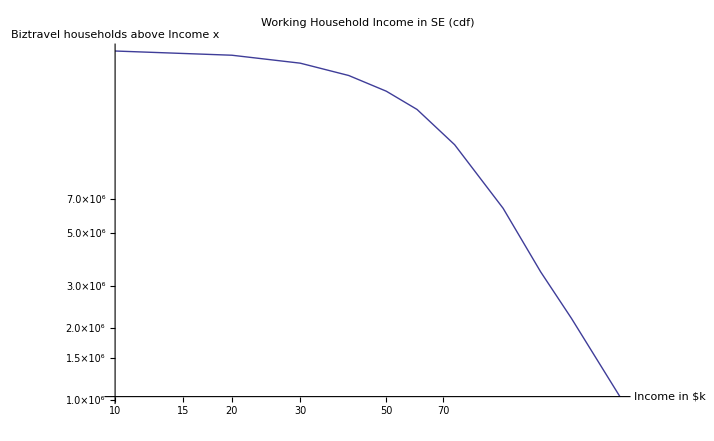

```mathematica
ListLogLogPlot[plotpts,Joined->True,PlotLabel->"Working Household Income in SE (cdf)",AxesLabel->{"Income in $k","Biztravel households above Income x"}]
```

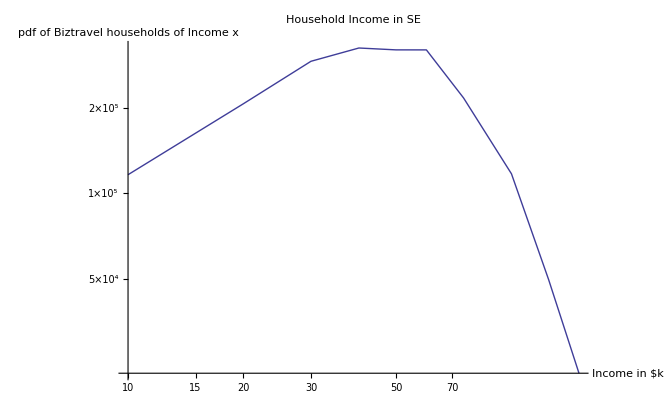

```mathematica
ListLogLogPlot[pdfbiz,Joined->True,PlotLabel->"Household Income in SE",AxesLabel->{"Income in $k","pdf of Biztravel households of Income x"}]
```

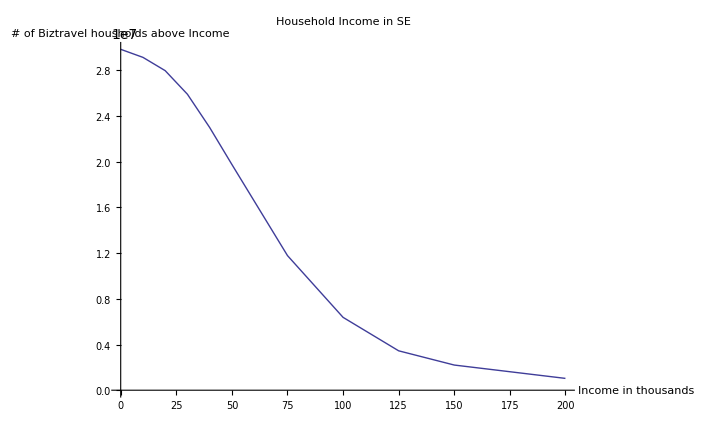

```mathematica
ListPlot[plotpts,Joined->True,PlotLabel->"Household Income in SE",AxesLabel->{"Income in thousands","# of Biztravel housholds above Income"}]
```

A little exploratory data analysis for the lower part of the distribution, showing that a quadratic exponential is a good and simple fit.

```mathematica
loglinearplotpts=Table[{plotpts[[i,1]],Log[plotpts[[i,2]]]},{i,9}]
llpp=Fit[loglinearplotpts,{1,x,x^2},x]
```

{{0.,17.2113},{10.,17.1874},{20.,17.1467},{30.,17.07},{40.,16.9509},{50.,16.7991},{60.,16.623},{75.,16.2822},{100.,15.6681}}

17.2208-0.00123066 x-0.000144571 x^2

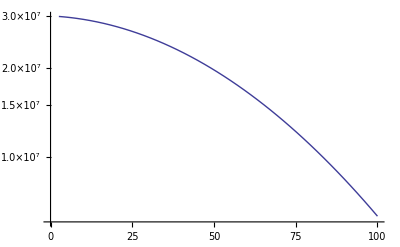

```mathematica
curvec=LogPlot[Exp[llpp],{x,0,100},PlotRange->{{0,100},{6000000,30000000}}]
```

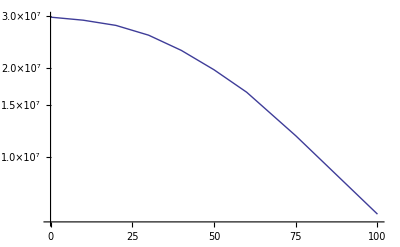

```mathematica
curvea=ListLogPlot[Take[plotpts,9],Joined->True,PlotRange->{{0,100},{6000000,30000000}}]
```

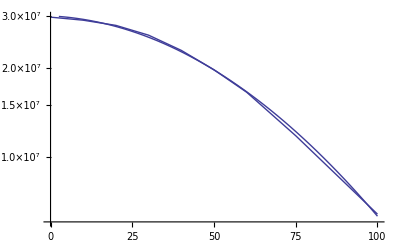

```mathematica
Show[curvea,curvec]
```

Separate out the power law part of the data, which is income >= $75k.  Pretty amazing, the 2001 IRS data exponent is -1.942  (the cdf will have the pdf exponent plus 1).  This gives a steeper slope, but the power law flattens out at the upper end somewhat, and the 2001 data included higher categories, so this is a slightly more conservative estimate for the average..

```mathematica
<<"LinearRegression`"
```

```mathematica
regexp=Regress[Log[Take[plotpts,-5]],{1,x},x]
```

{ParameterTable→ | Estimate | SE | TStat | PValue
1 | 27.1288 | 0.29796 | 91.0485 | 2.92054×10^-6
x | -2.50155 | 0.0617703 | -40.4976 | 0.0000331307,RSquared→0.998174,AdjustedRSquared→0.997566,EstimatedVariance→0.00215025,ANOVATable→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 1 | 3.52653 | 3.52653 | 1640.05 | 0.0000331307
Error | 3 | 0.00645076 | 0.00215025 |  | 
Total | 4 | 3.53298 |  |  | }

2007 Addendum:  Slope is less when we filter for working age households.  This may change DJ results quite a lot.  It is entirely possible a lot of wealth polarization has compounded this effect between 2001 data and 2006 data.

```mathematica
avgexp=regexp[[1,2,1,2,1]]
```

-2.50155

Now calculate the exponent for each grid square.  The numbers will not be stable enough unless there's at least at least three households in the grid square with >= $200k income, filter out entries where those are less.

Tail is used to  to draw purely from the power law. (>=$100k)  $75k to $100k is in the superposition region, and the power law will be used in concert with the quadratic exponential here.

```mathematica
gridinc=bizincomepops;
```

```mathematica
Do[gridinc[[i,j]]=trpropensity[[j]] gridinc[[i,j]],{i,Length[gridinc]},{j,12}];
```

```mathematica
Dimensions[gridinc]
```

{10947,12}

```mathematica
grid2=Table[Part[gridcts[[i]],{1,2,3,4,24,25,26,27,28,29,30,31,32,33,34,35}],{i,2,Length[gridcts]}];
```

Here is for the old data format for DayJet

```mathematica
households=Table[Sum[gridinc[[i,j]],{j,1,12}],{i,Length[gridinc]}];
tail=Table[Sum[gridinc[[i,j]],{j,9,12}],{i,Length[gridinc]}];
low=Table[Sum[gridinc[[i,j]],{j,1,9}],{i,Length[gridinc]}];
wealthy=Table[gridinc[[i,12]],{i,Length[gridinc]}];
```

Here is for the new data format for NGAero

```mathematica
households=Table[Sum[grid2[[i,j]],{j,5,16}],{i,Length[grid2]}];
tail=Table[Sum[grid2[[i,j]],{j,13,16}],{i,Length[grid2]}];
low=Table[Sum[grid2[[i,j]],{j,5,13}],{i,Length[grid2]}];
wealthy=Table[grid2[[i,16]],{i,Length[grid2]}];
```

```mathematica
hhcountlift=Table[If[households[[i]]==0,1,grid2[[i,4]]/households[[i]]],{i,Length[grid2]}];
```

```mathematica
Mean[hhcountlift]//N
```

1.31733

```mathematica
avglowprop=1-weightedcumulsums[[8]]/weightedcumulsums[[1]]//N
avgmidprop=(weightedcumulsums[[8]]-weightedcumulsums[[9]])/weightedcumulsums[[1]]//N
avghighprop=weightedcumulsums[[9]]/weightedcumulsums[[1]]//N
```

0.605075

0.181232

0.213693

First, create a fit to the poorly sampled grid squares and use the characteristic distributions of their sum to represent all poorly sampled grid squares.

Now fit all of the grid squares, defaulting to the above for the low population/sparse statistics grid squares. Now do the "gerrymander" calculation for the population that is non-zero but doesn't have enough people to fit a full curve to each grid square.  Sum them into one "supersquare".

```mathematica
tailexponentplot[j_]:=If[wealthy[[j]]≥3,
D[Fit[Log[tailsums[[j]]],{1,x},x],x],0]
```

```mathematica
tailexponentmodel[j_]:=If[wealthy[[j]]≥3,
D[Fit[Log[tailsums[[j]]],{1,x},x],x],-3.598]
```

```mathematica
lowpartialset[j_]:=Table[{income[[i-4]],Log[Sum[grid2[[j,k]],{k,i,16}]]},{i,5,13}]
```

```mathematica
quadexp[points_]:={
rg1=Fit[points,{1,x,x^2},x];
rg2=Fit[points,{1,x^2},x];
If[Coefficient[rg1,x,1]≤0,{Coefficient[rg1,x,1],Coefficient[rg1,x,2]},{0,Coefficient[rg2,x,2]}]
}[[1]]
```

Here's the old DayJet calculation

```mathematica
gerrymanderset=DeleteCases[Table[If[wealthy[[i]]< 3, gridinc[[i]],0],{i,Length[gridinc]}],0];
Length[gerrymanderset]
Sum[gerrymanderset[[i,2]],{i,Length[gerrymanderset]}]
gerrysums=Table[Sum[gerrymanderset[[i,j]],{i,Length[gerrymanderset]}],{j,1,12}]
gerrycum=Table[Sum[gerrysums[[j]],{j,k,12}],{k,1,12}]
avgq=quadexp[Table[{income[[i]],Log[gerrycum[[i]]]},{i,9}]]
lowgerry=(gerrycum[[1]]-gerrycum[[8]])/gerrycum[[1]]//N
midgerry=(gerrycum[[8]]-gerrycum[[9]])/gerrycum[[1]]//N
highgerry=gerrycum[[9]]/gerrycum[[1]]//N
ri=Fit[Table[Log[{income[[i]],gerrycum[[i]]}],{i,8,12}],{1,x},x];
averagetau=ri[[1,2,1,2,1]]
```

```mathematica
grid2[[3423]]
```

{Hudspeth Draw,30100-D7,15,10,1,1,0,2,0,1,0,0,1,1,0,0}

```mathematica
gerrymanderset=DeleteCases[Table[If[wealthy[[i]]< 3, grid2[[i]],0],{i,Length[grid2]}],0];
Length[gerrymanderset]
Sum[gerrymanderset[[i,4]],{i,Length[gerrymanderset]}]
gerrysums=Table[Sum[gerrymanderset[[i,j]],{i,Length[gerrymanderset]}],{j,5,16}]
gerrycum=Table[Sum[gerrysums[[j]],{j,k,12}],{k,1,12}]
avgq=quadexp[Table[{income[[i]],Log[gerrycum[[i]]]},{i,9}]]
lowgerry=(gerrycum[[1]]-gerrycum[[8]])/gerrycum[[1]]//N
midgerry=(gerrycum[[8]]-gerrycum[[9]])/gerrycum[[1]]//N
highgerry=gerrycum[[9]]/gerrycum[[1]]//N
averagetau=D[Fit[Table[Log[{income[[i]],gerrycum[[i]]}],{i,8,12}],{1,x},x],x]
```

33487

3188708

{246911,291101,341373,342335,277418,237820,260711,210637,88873,32462,19765,11244}

{2360650,2113739,1822638,1481265,1138930,861512,623692,362981,152344,63471,31009,11244}

{-0.0138905,-0.000143057}

0.846237

0.0892284

0.0645348

-3.59753

Generate some descriptors of the amount of mass in each part of the distribution (low, high, and overlap) for all of the other grid squares

```mathematica
highprop=Table[If[wealthy[[i]]≥ 3,tail[[i]]/households[[i]], highgerry],{i,Length[grid2]}]//N;
midprop=Table[If[wealthy[[i]]≥ 3,Sum[ grid2[[i,j]],{j,12,12}]/households[[i]],midgerry],{i,Length[grid2]}]//N;
lowprop=Table[If[wealthy[[i]]≥ 3,Sum[ grid2[[i,j]],{j,5,11}]/households[[i]], lowgerry],{i,Length[grid2]}]//N;
```

Check to see that they always add to 1.

```mathematica
a1=Take[midprop,{2000,2020}]
a2=Take[highprop,{2000,2020}]
a3=Take[lowprop,{2000,2020}]
a1+a2+a3
```

{0.113924,0.0892284,0.112676,0.0892284,0.0892284,0.0892284,0.0892284,0.0892284,0.126984,0.0892284,0.0892284,0.0892284,0.0892284,0.0892284,0.0653595,0.0892284,0.0892284,0.0892284,0.107914,0.113636,0.0892284}

{0.0886076,0.0645348,0.150235,0.0645348,0.0645348,0.0645348,0.0645348,0.0645348,0.111111,0.0645348,0.0645348,0.0645348,0.0645348,0.0645348,0.0653595,0.0645348,0.0645348,0.0645348,0.153135,0.174242,0.0645348}

{0.797468,0.846237,0.737089,0.846237,0.846237,0.846237,0.846237,0.846237,0.761905,0.846237,0.846237,0.846237,0.846237,0.846237,0.869281,0.846237,0.846237,0.846237,0.738952,0.712121,0.846237}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
tailsums=Table[{{75,Sum[ grid2[[i,j]],{j,12,16}]},{100,Sum[ grid2[[i,j]],{j,13,16}]},{125,Sum[ grid2[[i,j]],{j,14,16}]},{150,Sum[ grid2[[i,j]],{j,15,16}]},{200,Sum[ grid2[[i,j]],{j,16,16}]}},{i,Length[grid2]}];
```

```mathematica
Length[tailsums]
```

54012

Plot up the tail exponents to see that the distribution is well behaved

```mathematica
exponents=DeleteCases[Table[tailexponentplot[i],{i,Length[tailsums]}],0];
```

```mathematica
Histogram[exponents, PlotLabel->"Tail Exponent Distribution", AxesLabel->{"Exponent","Number of Grid Squares"}]
```

-Graphics-

Compute the tail exponents for the purpose of modeling, putting in default for low statistics squares.

```mathematica
exponents=Table[tailexponentmodel[i],{i,Length[tailsums]}];
```

```mathematica
Take[exponents,100]
```

{-3.598,-3.598,-3.97322,-3.598,-2.86812,-3.598,-1.88208,-1.93044,-1.97688,-3.598,-3.598,-3.598,-3.598,-3.598,-2.02943,-2.0582,-3.598,-3.598,-3.598,-3.598,-3.598,-3.598,-2.04546,-2.16329,-3.598,-3.598,-3.598,-3.598,-3.598,-3.598,-2.81623,-2.81345,-3.10312,-3.598,-3.598,-3.598,-3.598,-3.598,-3.598,-2.11256,-2.76255,-2.30254,-3.598,-3.598,-3.598,-3.598,-3.598,-1.94577,-3.48635,-1.93344,-3.598,-3.598,-3.598,-3.598,-3.598,-3.598,-3.598,-2.87905,-3.598,-3.598,-3.598,-1.91778,-3.59255,-2.12242,-1.59867,-3.598,-2.95026,-2.24112,-1.78503,-2.41915,-2.09371,-3.598,-3.598,-1.88162,-2.40053,-3.598,-3.598,-1.53576,-3.598,-3.598,-2.30761,-3.598,-1.96487,-2.36589,-2.35722,-2.2562,-3.09007,-2.48146,-1.92715,-3.598,-2.10923,-1.4346,-2.04391,-2.49689,-2.5616,-1.98553,-3.598,-3.598,-3.598,-1.24248}

Use a log-linear function and fit a quadratic function to the grid squares below $100k. The fit is quite good!  The reason for this choice of function is rapid analytic reverse sampling.  A better fit could be had, but sampling it would be numerical and much slower.

```mathematica
lowpartialset[33]
```

{{0,Log[3148]},{10,Log[2588]},{20,Log[2200]},{30,Log[1841]},{40,Log[1461]},{50,Log[1228]},{60,Log[939]},{75,Log[648]},{100,Log[368]}}

```mathematica
quadexp[lowpartialset[33]]
```

{-0.01735,-0.000042953}

```mathematica
grid2[[33]]
```

{Mountain View,19155-E1,7286,3814,560,388,359,380,233,289,291,280,206,95,30,37}

```mathematica
tt=Table[{income[[i]],Log[gerrycum[[i]]]},{i,9}]
```

{{0,Log[2360650]},{10,Log[2113739]},{20,Log[1822638]},{30,Log[1481265]},{40,Log[1138930]},{50,Log[861512]},{60,Log[623692]},{75,Log[362981]},{100,Log[152344]}}

```mathematica
rg1
```

8.05511-0.01735 x-0.000042953 x^2

```mathematica
rg2
```

7.75678-0.000204521 x^2

```mathematica
Coefficient[rg1,x,2]
```

-0.000042953

```mathematica
avgq=quadexp[tt]
```

{-0.0138905,-0.000143057}

```mathematica
qvector=Table[If[grid2[[i,16]]>=3,quadexp[lowpartialset[i]], avgq],{i,Length[grid2]}];
```

Generate a scatterplot of all of the coefficients of the low end of the income distribution to see if it is well behaved.  It seems to be.

```mathematica
Length[tauvector]
```

```mathematica
Length[exponents]
```

54012

```mathematica
lowprop[[1]]
```

0.846237

```mathematica
gridcts[[32]]
```

{Kaunene,19155-D7,764,365,103,16,55200,-155.812,19.4375,15,Hawaii,,,25900,Hilo, HI Micro,53,68,22,8,350.78,94.01,2192.74,544.66,27,25,40,35,26,25,30,36,20,10,10,5}

```mathematica
households[[1]]
```

23

```mathematica
{"NAME","KEY","ADULTCY","HHDCY","BUSCYEMP","BUSCYEST","INCCYAVEHH","CentroidX","CentroidY","KEY_STATE","NAME_STATE","KEY_METRO_CBSA","NA2E_METRO_CBSA","KEY_MICRO_CBSA","NAME_MICRO_CBSA","IND00FOOD","IND00CONS","IND00PUBA","IND00REAL","XCYTR801","XCYTR803","XCYTR5","XCYTR8","HHIncLessthan10K","HHinc10K20K","HHinc20K30K","HHinc30K40K","HHinc40K50K","HHinc50K60K","HHinc60K75K","HHinc75K100K","HHinc100K125K","HHinc125K150K","HHinc150K200K","HHinc200Kplus"}
```

```mathematica
modelvector[[123]]
```

{WAIALEALE                HI,21159-H4,-159.437,21.9375,0.62424,0.166377,0.209383,-0.00486758,-0.000108378,-2.16791}

```mathematica
gridcts[[2]]
```

{Ka Lae (digital),18155-H6,54,28,119,19,42410,-155.687,18.9375,15,Hawaii,,,25900,Hilo, HI Micro,2,3,0,1,288.84,77.65,1860.25,448.95,5,4,2,3,2,2,2,1,1,0,0,1}

```mathematica
modelvector=Table[{grid2[[i,1]],grid2[[i,2]],gridcts[[i+1,8]],gridcts[[i+1,9]],lowprop[[i]],midprop[[i]],highprop[[i]],exponents[[i]],qvector[[i,1]],qvector[[i,2]]},{i,Length[grid2]}];
```

```mathematica
SetDirectory["/Users/brucesawhill/Desktop"]
```

/Users/brucesawhill/Desktop

```mathematica
Export["ModelVector.xls",modelvector];
```

```mathematica
Length[grid2]
```

54012

```mathematica
grid2[[1]]
```

{Ka Lae (digital),18155-H6,54,28,5,4,2,3,2,2,2,1,1,0,0,1}

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},w] plots a histogram with bin width specification w.
Histogram[{x_1,x_2,…},w,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

```mathematica
Histogram3D[qvector]
```

-Graphics3D-

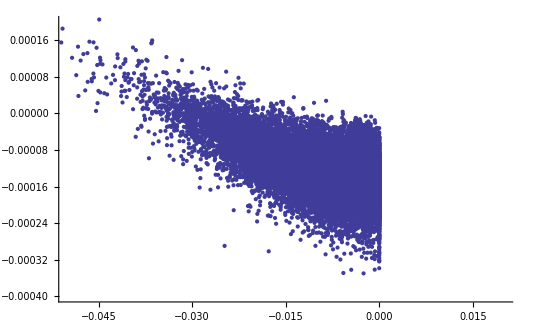

```mathematica
ListPlot[qvector,PlotRange->{{-.05,0.02},{-.0004,0.0002}}]
```

```mathematica
tauvector[[36]]
```

{-0.001723,-0.000185586}

```mathematica
Sum[If[tauvector[[i,1]]<0, households[[i]],0],{i,Length[households]}]
```

1.52987×10^7

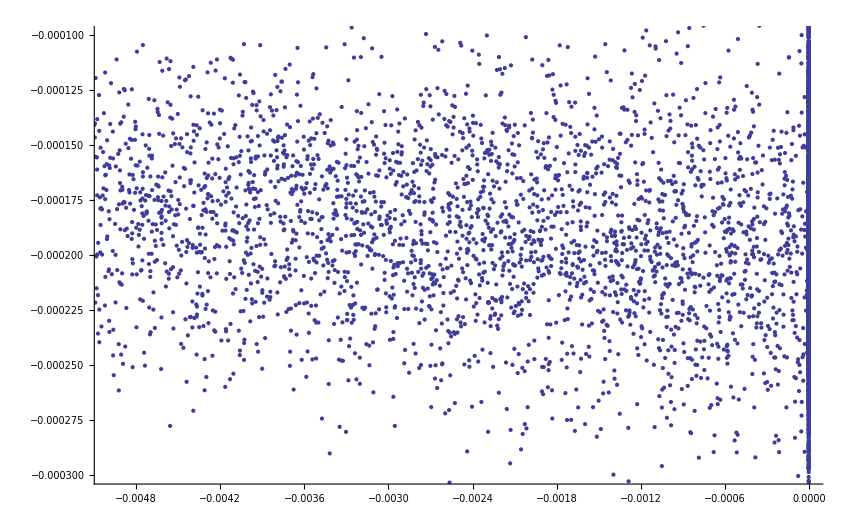

```mathematica
ListPlot[tauvector,PlotRange->{{-.005,0},{-.0003,-.0001}}]
```

```mathematica
grandtable=Table[{lowprop[[i]],midprop[[i]],highprop[[i]],exponents[[i]],tauvector[[i,1]],tauvector[[i,2]]},{i,Length[gridinc]}];
SetDirectory["/Users/brucesawhill/Desktop/DayJetDesktop"]
Export["HHincomedistributionfits2007.txt", grandtable, "CSV"]
```

/Users/brucesawhill/Desktop/DayJetDesktop

HHincomedistributionfits2007.txt

```mathematica
Take[grandtable,16]
```

{{0.7653,0.144724,0.0899768,-4.11393,-0.00228585,-0.00022149},{0.554525,0.21029,0.235185,-2.53236,0,-0.000144753},{0.764366,0.128779,0.106856,-2.81753,-0.00471281,-0.000184323},{0.571929,0.211236,0.216835,-2.75907,-0.0000439969,-0.000150984},{0.794523,0.100916,0.104561,-2.35547,-0.00693479,-0.00017119},{0.7653,0.144724,0.0899768,-4.11393,-0.00228585,-0.00022149},{0.471398,0.215834,0.312768,-3.01253,0,-0.000116328},{0.7653,0.144724,0.0899768,-4.11393,-0.00228585,-0.00022149},{0.7653,0.144724,0.0899768,-4.11393,-0.00228585,-0.00022149},{0.713978,0.161434,0.124589,-2.52617,0,-0.000212908},{0.700285,0.1751,0.124616,-2.72786,-0.00173159,-0.000190707},{0.734545,0.125334,0.14012,-2.67325,-0.00637765,-0.000141477},{0.7653,0.144724,0.0899768,-4.11393,-0.00228585,-0.00022149},{0.814936,0.102416,0.0826484,-2.23728,-0.00678475,-0.000193094},{0.7653,0.144724,0.0899768,-4.11393,-0.00228585,-0.00022149},{0.632868,0.178698,0.188434,-3.29095,-0.0016658,-0.000152539}}

```mathematica
driverlist[[1]]
```

{Acworth,33094-G8,186,93,5,2,40783,-94.9375,33.8125,*40,*Oklahoma,0,0,0,0,7,4,5,1,275.96,74.04,1848.78,428.81,6,13,12,6,5,8,10,4,2,0,1,0,4130,6938}

## Sources and Sinks

Now we should be able to calculate the prorated weights for sources and sinks.  I'll use the 50-mile radius as the "travel-generation" radius that characterizes how much people in a given area have to do long distance travel (out of the region) to get resources not available inside of the circle.

```mathematica
Dimensions[driverlist]
```

{10947,37}

```mathematica
Do[If[driverlist[[i,j]]=="",driverlist[[i,j]]=0],{i,Length[driverlist]},{j,Length[driverlist[[i]]]}];
```

```mathematica
sourceweights=Table[driverlist[[i,37]]^0.63 driverlist[[i,17]]/If[driverlist[[i,37]]==0,1,driverlist[[i,37]]],{i,Length[gridinc]}];
```

```mathematica
(*sourceweights=Table[driverlist[[i,37]]^0.63 driverlist[[i,17]] propensityweights[[i]]/If[driverlist[[i,37]]==0,1,driverlist[[i,37]]],{i,Length[gridinc]}];*)
```

```mathematica
sinkweights=Table[driverlist[[i,36]]^0.55 driverlist[[i,16]]/If[driverlist[[i,36]]==0,1,driverlist[[i,36]]],{i,Length[gridinc]}];
```

```mathematica
normsourceweights=sourceweights/Plus@@sourceweights;
```

```mathematica
normsinkweights=sinkweights/Plus@@sinkweights;
```

```mathematica
unitysourceweights=Length[gridinc] normsourceweights;
```

```mathematica
unitysinkweights= Length[gridinc] normsinkweights;
```

```mathematica
bigtable=Table[{driverlist[[i,2]],sourceweights[[i]],normsourceweights[[i]],unitysourceweights[[i]],sinkweights[[i]],normsinkweights[[i]],unitysinkweights[[i]]},{i,Length[gridinc]}];
```

```mathematica
driverlist[[1]]
```

{Acworth,33094-G8,186,93,5,2,40783,-94.9375,33.8125,*40,*Oklahoma,0,0,0,0,7,4,5,1,275.96,74.04,1848.78,428.81,6,13,12,6,5,8,10,4,2,0,1,0,4130,6938}

```mathematica
bigtable[[1]]
```

{33094-G8,0.151636,2.68111×10^-6,0.0293501,0.165166,7.64802×10^-6,0.0837229}

```mathematica
Export["sourcesinkweights.txt", bigtable, "CSV"]
```

sourcesinkweights.txt

There are still plenty of grid squares left after the filtering process.  The ones that aren't populous enough will just use average data.  THis section superseded by the idea of aureoles.  (50 mile radius circles around grid squares)

```mathematica
crowdedsquares=DeleteCases[Table[If[ driverlist[[3 i -2,13]]≥10,driverlist[[3 i-2]],0],{i,Length[gridinc]}],0];
Length[crowdedsquares]
```

4909

```mathematica
sixsums=Table[Sum[crowdedsquares[[i, j]],{j, 8, 13}],{i,Length[crowdedsquares]}];
wealthos=Table[crowdedsquares[[i,13]],{i,Length[crowdedsquares]}];
logratios=Table[Log[sixsums[[i]]/wealthos[[i]]],{i,Length[crowdedsquares]}]//N;
```

```mathematica
<<Statistics`DataManipulation`
```

```mathematica
bcs=BinCounts[logratios,{0.2,5,0.2}]
BarChart[bcs]
```

{0,5,9,16,26,80,165,242,335,524,629,665,625,561,374,288,179,99,49,24,10,2,2,0}

⁃Graphics⁃

This is quite interesting.  The exponent varies a lot, and it does in a way that looks suspiciously Gaussian.

It is going to require substantial changes to the model to incorporate different exponents for each grid square at the moment. so kludge it by introducing a multiplier instead.

```mathematica
multipliers=Table[If[driverlist[[3 i -2,2]]==0,0,Sum[driverlist[[3 i -2,j]],{j,8,13}]/driverlist[[3 i -2,2]]],{i,Length[gridinc]}];
```

```mathematica
BinCounts[multipliers,{0,1.1,0.01}]
```

{32,213,727,1662,2032,1776,1278,843,540,369,246,187,112,128,76,59,54,52,40,29,28,16,10,3,2,5,3,1,0,1,1,0,1,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
hhnorm=8195300/34506507
```

8195300/34506507

```mathematica
incomemults=1/hhnorm multipliers;
```

```mathematica
bcmult=BinCounts[incomemults,{0,1.0,0.02}];
BarChart[bcmult]
```

⁃Graphics⁃

A very lognormal kind of distribution, not centered around 1.0.  Most places are poorer and the wealthy are concentrated in a small number of areas, probably ones with more than average population as well.  Note that the "wealth multipliers" are not weighted by population.   Weight by population will by definition give 1.0.  This might be a new result, associated with the product of random numbers--cascding dependent probabilities of luck in life as expressed in geography..